```mathematica
MINISTERUL EDUCAȚIEI ȘI CERCETĂRII AL REPUBLICII MOLDOVA

Universitatea Tehnică a Moldovei

Facultatea Calculatoare,Informatică şi Microelectronică

Departamentul Informatică şi Ingineria Sistemelor









RAPORT

Lucrare de laborator nr.1

la cursul „Probabilitate și statistică aplicată”









A efectuat:                                              St.gr.CR-221FR Serba Cristina

A verificat:                                                 Andrievschi-Bagrin Veronica













Chișinău 2023
```

1)Să se construiască o expresie aritmetică care conţine cele patru
operaţii aritmetice, ridicarea la putere, fracţii şi paranteze. 2)Să se
determine valoarea exactă a expresiei construite. 3)Să se determine o
careva valoare aproximativă. 4)Să se determone o valoare aproximativă
care conţine 20 cifre semnificative.

```mathematica
(2^2+(2+3^2)-2*3)/(100-20)
```

9/80

```mathematica
(2^2+(2+3^2)-2*3)/(100-20)//N
```

0.1125

```mathematica
N[(2^2+(2+3^2)-2*3)/(100-20),20]
```

0.1125

```mathematica
N[Pi,21]
```

3.14159265358979323847

Să se dezvolte în produs de factori expresia x^n1, unde n este egal cu
10 plus numărul variantei.

```mathematica
Factor[x^31-1]
```

(-1+x) (1+x+x^2+x^3+x^4+x^5+x^6+x^7+x^8+x^9+x^10+x^11+x^12+x^13+x^14+x^15+x^16+x^17+x^18+x^19+x^20+x^21+x^22+x^23+x^24+x^25+x^26+x^27+x^28+x^29+x^30)

Fiind date două matrice A şi B, a=data nașterii, b=luna nașterii, număr
α=numărul de ordine din registru, să se determine : 1)αA ; 2)A+B ; 3)AB ;
4)detA ; 5)A^(-1)

```mathematica
A = {{10,-1,2},{4,7,-3},{-5,2,1}}
```

{{10,-1,2},{4,7,-3},{-5,2,1}}

```mathematica
B= {{0,-2,1},{1,10,3},{3,1,7}}
```

{{0,-2,1},{1,10,3},{3,1,7}}

```mathematica
MatrixForm[21*A]
```

(210 | -21 | 42
84 | 147 | -63
-105 | 42 | 21)

```mathematica
MatrixForm[A+B]
```

(10 | -3 | 3
5 | 17 | 0
-2 | 3 | 8)

```mathematica
MatrixForm[A.B]
```

(5 | -28 | 21
-2 | 59 | 4
5 | 31 | 8)

```mathematica
Det[A]
```

205

```mathematica
Inverse[A]//MatrixForm
```

(13/205 | 1/41 | -11/205
11/205 | 4/41 | 38/205
43/205 | -3/41 | 74/205)

Să se rezolve sistemul de ecuaţii liniare, n=numărul de ordine din
registru

```mathematica
Solve[{21*x+(2*21-1)*y+(21-5)*z==(21-4),x+3*21*y-(7-21)*z==-2*21-5,2*21*x-(21+2)*y+(21-3)*z==6*21-1},{x,y,z}]
```

{{x→2,y→-1,z→1}}

Să se calculeze limitele

```mathematica
Limit[(x^2+(1-21)*x-21)/(x^2-n^2), x->21]
```

0

```mathematica
Limit[((21*n+7)/21*n+8)^((21-15)*x), x->Infinity]
```

ConditionalExpression[∞, Log[8+n/3+n^2]>0]

Să se calculeze integralele

```mathematica
Integrate[Sqrt(21-x^2),x]
```

-Sqrt (-21 x+x^3/3)

```mathematica
Integrate[((21+1)*x^3)/(21+x^8),{x,0,1}]
```

(11 ArcTan[1/(√21)])/(2 √21)

Să se construiască graficul funcțiilor :

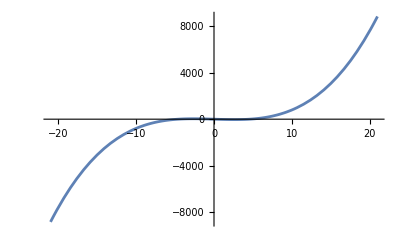

```mathematica
Plot[x^3-21*x,{x,-21,21}]
```

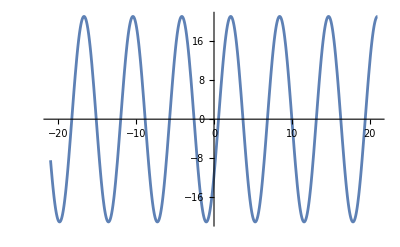

```mathematica
Plot[21*Cos[x-21],{x,-21,21}]
```

Să se reprezinte grafic o suprafață cu ajutorul funcției Plot3D,
folosind/inspirându-vă din exemplele din Help

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-